```mathematica
SetDirectory[NotebookDirectory[]];
(Module[{},Unprotect[#];Options[#]=Options[#]~Union~{ImageSize->{600,600/GoldenRatio}}])&/@{Graphics,ListPlot,Plot,ListLogPlot};
(*TODO:
*)
```

```mathematica
(*
a=(TimeConstrained[FactorInteger@RandomInteger[{2^500,2^501}],5]//Timing)&/@Range[5500];
*)
```

```mathematica
a=<<"factors";

aOK=Cases[a,{_?NumericQ,Except[$Aborted]},1]//Length
aAB=Cases[a,{_?NumericQ,$Aborted},1]//Length
aOK/(aAB+aOK)//N
```

1108

4392

0.201455

```mathematica
(*Jenom zkouška jak rychle to faktorizuje*)
w=77;
p=RandomPrime[{2^w,2^(w+1)}];
q=RandomPrime[{2^w,2^(w+1)}];
TimeConstrained[FactorInteger@(p*q),5]
```

{{212643052199886973899107,1},{251639307955322525473421,1}}

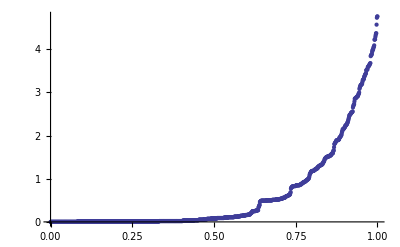

```mathematica
oks=Cases[a,{_?NumericQ,Except[$Aborted]},1];
casy = oks/.{e_,{___}}->e;
ListPlot[Sort[casy],DataRange->{0.,1.},PlotRange->All ]
(*y: straveny cas faktorizaci.*)
```

5.69946

4.94675

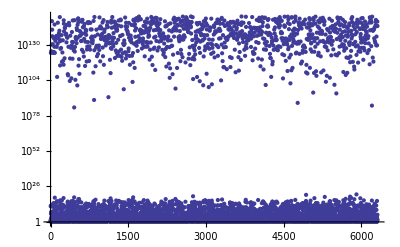

```mathematica
factorss=oks/.{_?NumericQ, e_}->e;
rozepis[{p_,n_}]:=Table[p,{i,n}]
rozloz[l_]:=Flatten[rozepis/@l]
factorss=rozloz/@factorss;(*seznamy factoru*)
factorssf=Flatten@factorss;
Length[factorssf]/aOK//N(* pocet faktoru, PrimeOmega= ~ LogLog[n]+B *)
((Union/@factorss)//Flatten//Length)/aOK//N (* pocet unikatnich faktoru (PrimeNu) *)
ListLogPlot[factorssf]
(*y: velikost faktoru,*)
```

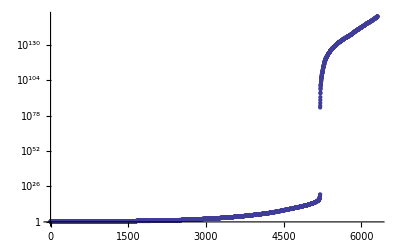

```mathematica
ListLogPlot[Sort[factorssf]]
(*To samy, akorat setrizeny*)
```

500.853

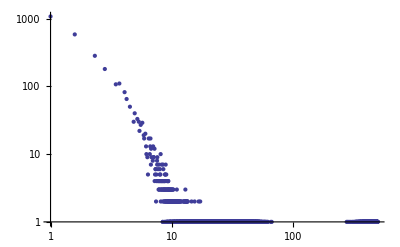

```mathematica
poctyfaktoru=Tally@factorssf/.{e_,r_}->{Log[2.,e],r};
m=Max[Transpose[poctyfaktoru][[1]]]
ListLogLogPlot[poctyfaktoru, DataRange->{2.,5.}]
(* pocty bitu v faktoru vs. jejich pocet *)
```

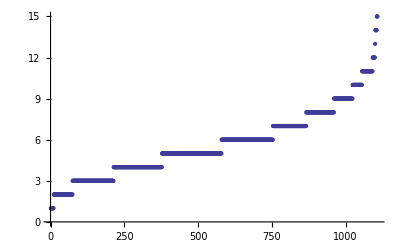

```mathematica
ListPlot[Sort[Length/@factorss]]
(*pocty faktoru*)
```